quad diagram

{2,1,5,5,1,1,1,0.01,0.01}

{{0,0},{0,1},{1,0},{0,10},{10,10},{5,5},{4,11/2},{6,11/2}}

{{0,10},{10,10},{5,5}}

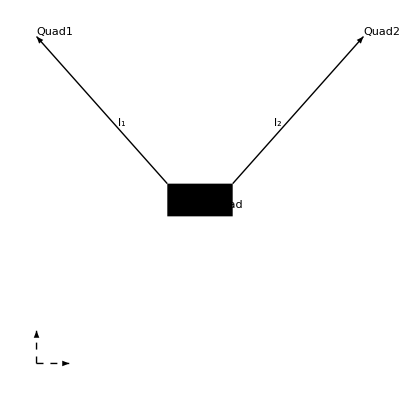

```mathematica
(*geometric properties:*)
{Subscript[l, p]=2, (* length of payload box *)
Subscript[h, p]=1, (* hight of payload box *)
Subscript[l, 1]=√25,
Subscript[l, 2]=√25,
Subscript[m, 1]=1,Subscript[m, 2]=1,Subscript[m, p]=1,
Subscript[k, 1]=1/100.,
Subscript[k, 2]=1./100
}
(*locations:*)
{Iorigin={0,0},
IaxisX = {0,1},
IaxisZ = {1,0},
Quad1CenterPos = {Subscript[x, i],Subscript[z, i]} /. i->1,
Quad2CenterPos = {Subscript[x, i],Subscript[z, i]} /. i->2,
PayloadCenterPos = {Subscript[x, i],Subscript[z, i]} /. i->p,
HangPoint1=PayloadCenterPos-{Subscript[l, p]/2,-Subscript[h, p]/2},
HangPoint2=PayloadCenterPos+{Subscript[l, p]/2,Subscript[h, p]/2}}
(*initial locations:*)
scale0 = 10;
{{Subscript[x, 1]=0,Subscript[z, 1]=scale0},{Subscript[x, 2]=scale0,Subscript[z, 2]=scale0},{Subscript[x, p]=scale0/2,Subscript[z, p]=scale0/2}}

(*labels*)
PayloadLabel =Text["Payload",{Subscript[x, i],Subscript[z, i]} /. i->p,{-1,2.5(+1+Subscript[h, p]/2)}];
Quad1Label =Text["Quad1",{Subscript[x, i],Subscript[z, i]} /. i->1,{-1,-1}];
Quad2Label =Text["Quad2",{Subscript[x, i],Subscript[z, i]} /. i->2,{-1,-1}];
l1Label=Text["l_1",{(Subscript[x, 1]+Subscript[x, p])/2,(Subscript[z, 1]+Subscript[z, p])/2},{-2,1}];
l2Label=Text["l_2",{(Subscript[x, 2]+Subscript[x, p])/2,(Subscript[z, 2]+Subscript[z, p])/2},{2,1}];
(*elements:*)
Iarrows={Dashed,Arrowheads[Small],Arrow[{Iorigin,IaxisX}],Arrow[{Iorigin,IaxisZ}]};
Labels = {PayloadLabel,Quad1Label,Quad2Label,l1Label,l2Label};
Cabels ={Arrowheads[{-Small,Small}],Arrow[{HangPoint1,Quad1Pos}],Arrow[{HangPoint2,Quad2Pos}]};
PayloadBox={Rectangle[HangPoint1-{0,Subscript[h, p]},HangPoint2]};
a=Graphics[{Iarrows,Labels,Cabels,PayloadBox}]
```

```mathematica
spring[r_: {1,0},n_: 20,w_: 1,origin_:{0,0}]:=Line@Transpose[{r-origin,-Cross[r-origin]}.{(#-1)/(2 n),Re[I^#] w/Norm[r-origin]}+origin]&@Range[2 n+1];
spr1=spring[r/.r->{3,5},n/.n->8,1,origin/.origin->{0,0}]
spr2=spring[r/.r->{3,5},n/.n->8,1,origin/.origin->{1,1}]
Graphics[{spr1,spr2},PlotRange->5]
Manipulate[Graphics[spring[r],PlotRange->5],{{r,{1,5}},Locator}]
```

Line[{{0,0},{3/16-5/(√34),5/16+3/(√34)},{3/8,5/8},{9/16+5/(√34),15/16-3/(√34)},{3/4,5/4},{15/16-5/(√34),25/16+3/(√34)},{9/8,15/8},{21/16+5/(√34),35/16-3/(√34)},{3/2,5/2},{27/16-5/(√34),45/16+3/(√34)},{15/8,25/8},{33/16+5/(√34),55/16-3/(√34)},{9/4,15/4},{39/16-5/(√34),65/16+3/(√34)},{21/8,35/8},{45/16+5/(√34),75/16-3/(√34)},{3,5}}]

Line[{{1,1},{9/8-2/(√5),5/4+1/(√5)},{5/4,3/2},{11/8+2/(√5),7/4-1/(√5)},{3/2,2},{13/8-2/(√5),9/4+1/(√5)},{7/4,5/2},{15/8+2/(√5),11/4-1/(√5)},{2,3},{17/8-2/(√5),13/4+1/(√5)},{9/4,7/2},{19/8+2/(√5),15/4-1/(√5)},{5/2,4},{21/8-2/(√5),17/4+1/(√5)},{11/4,9/2},{23/8+2/(√5),19/4-1/(√5)},{3,5}}]